```mathematica
<<AlexTools`ALXTools`
<<Spike2`FileCheck`
<<TwoTone`DP`
(*expDir="C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\images\\all figures\\";*)
expDir="C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\images\\article figures\\Nature submission 2\\raw_svg_figures\\";
imageRes=450;
```

```mathematica
Clear[confInter,rescaler]
confInter[data_,number_:1,confInterval_:1.96]:=If[data!={},Table[{#[[1]],#[[2]]+sign confInterval/(√number)#[[3]]}&/@data,{sign,{1,-1}}],{}];
rescaler[data_]:=If[data!={},{data[[;;,1]],Rescale[data[[;;,2]]],data[[;;,3]]}ᵀ,{}]

sRate = 20000;

{tickSizeMinor,tickSizeMajor}=Scaled[#]&/@{0.008,0.04};
{tickSizeMinorY,tickSizeMajorY}=Scaled[#]&/@{0.008,0.02};
fticksX={Range[200,1000,200],Range[200,1000,200],{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksx=Select[Table[{i,"",{0,If[Mod[i,100]==0,tickSizeMajor,tickSizeMinor]}},{i,100,1000,50}],Not@MemberQ[fticksX[[;;,1]],#[[1]]]&];
fticksX=fticksX~Join~fticksx;
fticksY={{0.25,"",{0,tickSizeMinorY}},{0.75,"",{0,tickSizeMinorY}}}~Join~({{0,0.5,1},{0,0.5,1},{0,tickSizeMajorY}&/@Range[3]}ᵀ);

(*
(* the following is in case you want the ticks to run in multiples of 180 Hz *)
fticksX={Range[180,1000,180],Range[180,1000,180],{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksX2={Range[270,1000,180],(""&/@Range[270,1000,180]),{0,tickSizeMajor}&/@Range[5]}ᵀ;
fticksx=Select[Table[{i,"",{0,tickSizeMinor}},{i,90,1000,45}],Not@MemberQ[fticksX[[;;,1]]~Join~fticksX2[[;;,1]] ,#[[1]]]&];
fticksX=fticksX~Join~fticksx~Join~fticksX2;*)


PairedColors = {
   RGBColor[0.651, 0.807, 0.890],   (* #a6cee3 *)
   RGBColor[0.122, 0.471, 0.706],   (* #1f78b4 *)
   RGBColor[0.698, 0.875, 0.541],   (* #b2df8a *)
   RGBColor[0.200, 0.627, 0.173],   (* #33a02c *)
   RGBColor[0.984, 0.604, 0.600],   (* #fb9a99 *)
   RGBColor[0.890, 0.102, 0.110],   (* #e31a1c *)
   RGBColor[0.992, 0.749, 0.435],   (* #fdbf6f *)
   RGBColor[1.000, 0.498, 0.000],   (* #ff7f00 *)
   RGBColor[0.792, 0.698, 0.839],   (* #cab2d6 *)
   RGBColor[0.416, 0.239, 0.545],   (* #6a3d9a *)
   RGBColor[1.000, 1.000, 0.600],   (* #ffff99 *)
   RGBColor[0.694, 0.349, 0.157]    (* #b15928 *)
};

snsDeep = hexToRGB[#]&/@{"#4C72B0","#55A868","#EBAF3A","#D55E8C","#C44E52","#A8A8A8"};
Clear[em,fm,fm2]
ResourceFunction["PolygonMarker"];
(* empty marker *)
em[name_String, size_ : 7] := ResourceFunction["PolygonMarker"][name, Offset[size],
   {Dynamic@
     EdgeForm[{CurrentValue["Color"], JoinForm["Round"], AbsoluteThickness[2], Opacity[1]}], FaceForm[White]},
   ImagePadding -> 6];
(*filled marker*)
fm[name_String,size_:8]:=ResourceFunction["PolygonMarker"][name,Offset[size],EdgeForm[]];
(* lightly filled marker *)
fm2[name_String,size_:9,opacity_:0.75]:=ResourceFunction["PolygonMarker"][name,Offset@size,
{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[1]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],opacity]}];

fm3[name_String,size_:9,opacity_:0.75,edgeThickness_:2,edgeOpacity_:1]:=ResourceFunction["PolygonMarker"][name,Offset@size,
{Dynamic@EdgeForm[{CurrentValue["Color"],Opacity[edgeOpacity],AbsoluteThickness[edgeThickness]}],Dynamic@FaceForm@Lighter[CurrentValue["Color"],opacity]}];

allShapes=ResourceFunction["PolygonMarker"][All]

plotGrid = ResourceFunction["PlotGrid"];
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarSlim,FivePointedStarThick,DancingStar,DancingStarRight,DancingStarThick,DancingStarThickRight,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SixfoldPinwheel,SixfoldPinwheelRight,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,SevenfoldPinwheel,SevenfoldPinwheelRight,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

## Figure 1 - novel audibility regions

### Panel A

```mathematica
{col1T,col1TN}={Black,blue};
{col2T,col2TN}={Black,(*hexToRGB["#800020"]*)RGBColor@@({170,021,041}/255)};
{circle,uptriangle,diamond,square,downtriangle}=Charting`CommonDump`GraphicsOpenPlotMarkers[][[;;5]];
(*ChartElementData["PlotMarkers"]*)
op=.6;
op2=.4;
size=5;

AGAdata = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Anopheles_final data_seg_5_JSON.txt","RawJSON"];
AGAdata["numbers"]= <|"quies"->2-1,"wsso"->5-1,"sso"->10|>;
AGAdata2 = Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Anopheles_final data_seg_5_JSON.txt","RawJSON"];
AGAdata2["numbers"] = <|"quies"->1,"wsso"->6,"sso"->5|>;
AGAdata3=AGAdata;
Do[AGAdata3[tone,state]=Sort@(Mean/@GatherBy[AGAdata[tone,state]~Join~AGAdata2[tone,state],#[[1]]&]),{tone,Keys[AGAdata][[;;-2]]},{state,{"quies","wsso","sso"}}];
AGAdata3 = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Anopheles_final data_seg_COMBINED_OLD and NEW5_JSON.txt","RawJSON"];
AGAdata3["numbers"]= <|"quies"->3,"wsso"->10,"sso"->15|>;

AAEdata = Import["N:\\Storage Files\\UCL Data\\Aedes\\Aedes_final data_seg_5_JSON.txt","RawJSON"];
AAEdata["numbers"]= <|"quies"->1,"wsso"->1,"sso"->3|>;
CQUdata  = Import["N:\\Storage Files\\UCL Data\\Culex\\Culex_final data_seg_5_JSON.txt","RawJSON"];
CQUdata["numbers"]=<|"quies"->2-1,"wsso"->4,"sso"->0|>;
```

```mathematica
opts={Frame->True,
FrameTicks->{{fticksY,None},{fticksX,None}},
FrameStyle->Directive@{(*AbsoluteThickness[1],*)Black, FontSize->8,FontFamily->"Helvetica"},
LabelStyle->Directive@{(*Black,AbsoluteThickness[1],*)Black, FontSize->8,FontFamily->"Helvetica"},
PlotRange->{{50,1020},{-0.05,1.1}},
ImageSize->300};

pntSize = 3{1,1};
pntFillOpacity = {.7,0.6};
pntOpacity = {1,1};
confIntervalsOpacity = {0.2,0.3};
pointEdgeThickness = 0.8{1,1};


dat = AGAdata3;
aga1T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[dat[#1,mechCondition]],dat["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[dat[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser1T","nerve1T"},{hexToRGB["#222222"],snsDeep[[1]]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
aga2T=Table[Show[MapThread[{ListLinePlot[(MovingAverage[#,3]&/@confInter[rescaler[dat[#1,mechCondition]],dat["numbers",mechCondition]]),Filling->{1->{2}},PlotStyle->{Opacity[0]},FillingStyle->Directive@{#2,Opacity[#8]},opts],
ListPlot[rescaler[dat[#1,mechCondition]][[;;,{1,2}]],PlotStyle->{#2,Opacity[1]},Joined->True,PlotMarkers->{fm3[#3,#4,#5,#6,#7]}]}&,
{{"laser2T","nerve2T"},{hexToRGB["#222222"],(*hexToRGB["#CC3377"]*)snsDeep[[4]]},
{"Circle","Circle"},
pntSize,pntFillOpacity,pointEdgeThickness,pntOpacity,confIntervalsOpacity}]],{mechCondition,{"quies","wsso","sso"}}];
```

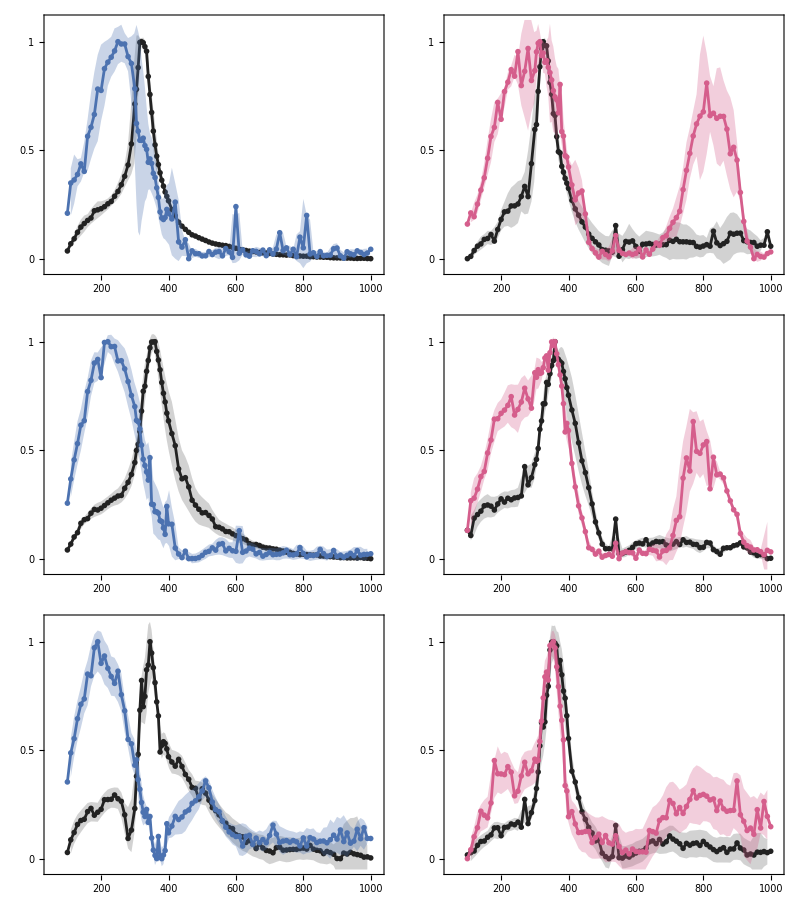

```mathematica
Grid[{aga1T,aga2T}ᵀ]
```

```mathematica
start = 5*4000;
len = 500;
plotRangeVal = 1{-.8,0.3};
{color1T,color2T} = {snsDeep[[1]],snsDeep[[4]]};
```

### Panel B

#### QUIES

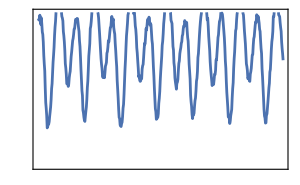
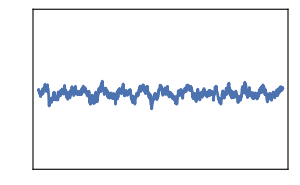
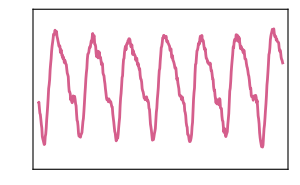
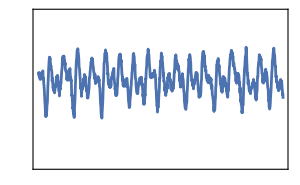
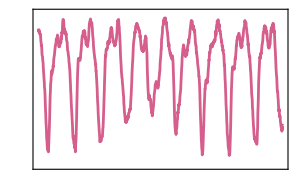

```mathematica
{nerve1Tquies260Hz,nerve1Tquies270Hz,nerve1Tquies350Hz,nerve1Tquies510Hz} =Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_017_(033).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_018_(035).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_031_(061).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_a_052_(103).txt"};

{nerve2Tquies350Hz,nerve2Tquies810Hz} = Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_b_031_(062).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_M_AGA_Kisumu_ZT13_2023-03-20_No 001_Nerve_b_082_(164).txt"};

quiesMin1T=Differences[MinMax[nerve1Tquies260Hz[[start;;start+5len]]]][[1]];
quiesMin2T=Differences[MinMax[nerve2Tquies350Hz[[start;;start+5len]]]][[1]];
len270 = 500;
{len510,offset510} = {1000,-500};
{len810,offset810}= {500,1000};
{{nquies270 = ListLinePlot[nerve1Tquies270Hz[[start;;start+len270]]/quiesMin1T ,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nquies510 = ListLinePlot[nerve1Tquies510Hz[[start+offset510;;start+offset510+len510]]/quiesMin1T -0.3,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nquies810 = ListLinePlot[nerve2Tquies810Hz[[start+offset810;;start+offset810+len810]]/quiesMin2T-0.2,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]},
{nquies1T350Hz = ListLinePlot[nerve1Tquies350Hz[[start+offset510;;start+offset510+len510]]/quiesMin1T -0.2,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nquies2T350Hz = ListLinePlot[nerve2Tquies350Hz[[start;;start+len510]]/quiesMin2T -0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]}}
```

#### wSSO

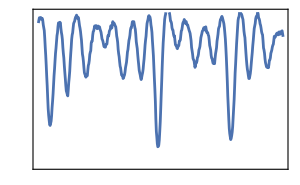
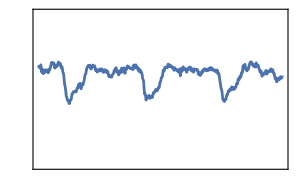
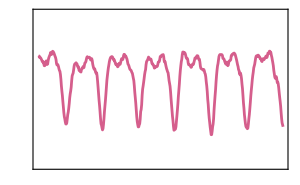
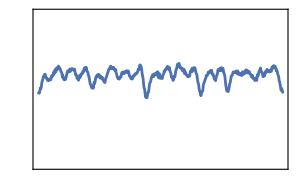
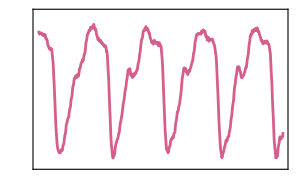

```mathematica
{nerve1TwSSO220Hz,nerve1TwSSO270Hz,nerve1TwSSO360Hz,nerve1TwSSO510Hz} =Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_013_(025).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_018_(035).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_033_(065).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_a_052_(103).txt"};

{nerve2TwSSO360Hz,nerve2TwSSO810Hz} = Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{
"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_b_033_(066).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito30\\set_1\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT05_2023-02-21_No 001_Nerve_b_082_(164).txt"};
wssoMin1T=Differences[MinMax[nerve1TwSSO220Hz[[start;;start+5len]]]][[1]];
wssoMin2T=Differences[MinMax[nerve2TwSSO360Hz[[start;;start+5len]]]][[1]];
len270 = 500;
{len510,offset510} = {500,-3450};
len810= 500;
{{nwsso270 = ListLinePlot[nerve1TwSSO270Hz[[start;;start+len270]]/wssoMin1T +0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nwsso510 = ListLinePlot[nerve1TwSSO510Hz[[start+offset510;;start+offset510+len510]]/wssoMin1T -0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nwsso810 = ListLinePlot[nerve2TwSSO810Hz[[start;;start+len810]]/wssoMin2T-0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]},
nwsso3601T =  ListLinePlot[nerve1TwSSO360Hz[[start;;start+len810]]/wssoMin1T-0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color1T,opts ],
nwsso3602T =  ListLinePlot[nerve2TwSSO360Hz[[start;;start+len810]]/wssoMin2T-0.1,Axes->False,PlotRange->plotRangeVal,FrameTicks->None,PlotStyle->color2T,opts ]}
```

#### SSO

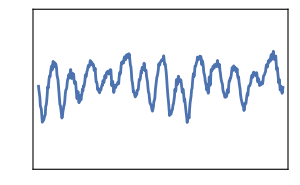
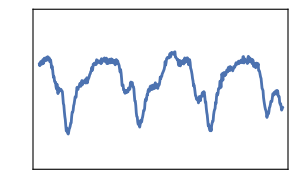
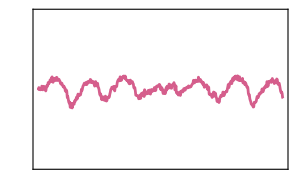
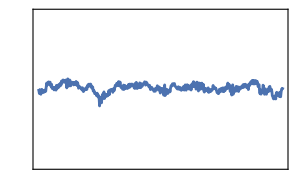
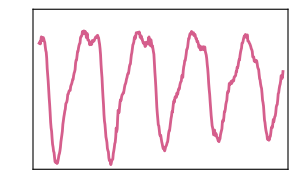

```mathematica
{nerve1TSSO190Hz,nerve1TSSO270Hz,nerve1TSSO355Hz,nerve1TSSO510Hz} =Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_010_(019).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_018_(035).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_032_(063).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_a_050_(099).txt"};
(*{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_a_010_(019).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_a_018_(035).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_a_052_(103).txt"};*)

{nerve2TSSO355Hz,nerve2TSSO810Hz} = Fold[HighpassFilter,readMyFile[#][[;;,2]],2π/sRate{60,60,60}]&/@{"N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_b_032_(064).txt","N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\Nerve\\Nerve_b_082_(164).txt"};
(*{"M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_b_032_(064).txt","M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito26\\set_2\\Nerve\\healthy_files\\M_AGA_Kisumu_ZT12_2023-02-16_No 001_Nerve_b_082_(164).txt"};*)
start = 5*4000;
len = 500;
offset =500;
yoffset=-0.2;
ssoMin1T=Differences[MinMax[nerve1TSSO190Hz[[start;;start+5len]]]][[1]];
ssoMin2T=Differences[MinMax[nerve2TSSO355Hz[[start;;start+5len]]]][[1]];

{{nsso270=ListLinePlot[nerve1TSSO270Hz[[start+offset;;start+len+offset]]/ssoMin1T+yoffset,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color1T,opts],
nsso510 = ListLinePlot[nerve1TSSO510Hz[[start+offset;;start+len+offset]]/ssoMin1T+yoffset,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color1T,opts]
(* NOTE: I am background removing the 540 Hz which dominates as crosstalk here!!! *),
nsso810=ListLinePlot[(nerve2TSSO810Hz-0.107Table[1.Cos[2π 540 t + 5π/24],{t,0,4.2,1/sRate}])[[start;;start+len]]/ssoMin2T-0.25,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color2T,opts]},
{nsso3551T = ListLinePlot[nerve1TSSO355Hz[[start+offset;;start+len+offset]]/ssoMin1T-0.25,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color1T,opts],
nsso3552T = ListLinePlot[nerve2TSSO355Hz[[start+offset;;start+len+offset]]/ssoMin2T+yoffset,PlotRange->plotRangeVal,Axes->False,FrameTicks->None,PlotStyle->color2T,opts]}}
```

### Panel C

```mathematica
ridgeDataSSO1T = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\0_overview\\M_AGA_G3_ZT13_2025-08-14_No 001_Laser and Nerve_overview_1T.txt","RawJSON"];
ridgeDataSSO2T = Import["N:\\Storage Files\\UCL Data\\Anopheles\\Mosquito 5\\set_1\\0_overview\\M_AGA_G3_ZT13_2025-08-14_No 001_Laser and Nerve_overview_2T.txt","RawJSON"];
rData1T = MovingAverage[#,4]&/@ridgeDataSSO1T["laser"][[;;,;;,{1,3}]];
rData1TN = MovingAverage[#,4]&/@ridgeDataSSO1T["nerve"][[;;,;;,{1,3}]];
rData2TNS = MovingAverage[#,4]&/@ridgeDataSSO2T["nerve"][[;;,;;,{1,3}]];

ridgeDataQUIES1T = Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\0_overview\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_Laser and Nerve_overview_1T.txt","RawJSON"];
ridgeDataQUIES2T = Import["M:\\Documents\\Alex\\UCL_data\\2022 - 2 tone\\Mosquito31\\set_1\\0_overview\\M_AGA_Kisumu_ZT13_2023-03-20_No 001_Laser and Nerve_overview_2T.txt","RawJSON"];

rData1TNQ = MovingAverage[#,4]&/@ridgeDataQUIES1T["nerve"][[;;,;;,{1,3}]];

rData2T = MovingAverage[#,4]&/@ridgeDataQUIES2T["laser"][[;;,;;,{1,3}]];
rData2TN = MovingAverage[#,4]&/@ridgeDataQUIES2T["nerve"][[;;,;;,{1,3}]];
```

```mathematica
hoffset = 90;
hoffsetL = 60;
voffset = 0.08
voffsetL =0.2;

(* 1T SSO nerve *)
ridge1T   = Table[MapAt[#+(i-1) hoffset&,rData1TN[[i]]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];
ridge1Ta = Table[MapAt[#+(i-1) hoffset&,Select[rData1TN[[i]],Between[#[[1]],{100,400}] &]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];
ridge1Tb = Table[MapAt[#+(i-1) hoffset&,Select[rData1TN[[i]],Between[#[[1]],{390,700}] &]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];
ridge1Tc = Table[MapAt[#+(i-1) hoffset&,Select[rData1TN[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData1TN[[i,;;,2]]] ,{All,1}],{i,Length@rData1TN}];

(* 1T SSO laser *)
ridge1TL   = Table[MapAt[#+(i-1) hoffsetL&,rData1T[[i]]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];
ridge1TaL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData1T[[i]],Between[#[[1]],{100,330-5i}] &]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];
ridge1TbL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData1T[[i]],Between[#[[1]],{325-5i,400+5i}] &]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];
ridge1TcL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData1T[[i]],Between[#[[1]],{390+5i,1000}] &]+ voffsetL (i)-Min[rData1T[[i,;;,2]]] ,{All,1}],{i,Length@rData1T}];

(* 2T SSO nerve *)
ridge2TS = Table[MapAt[#+(i-1) hoffset&,rData2TNS[[i]]+ voffset (i)-Min[rData2TNS[[i,;;,2]]] ,{All,1}],{i,Length@rData2TNS}];
ridge2TaS= Table[MapAt[#+(i-1) hoffset&,Select[rData2TNS[[i]],Between[#[[1]],{100,700}] &]+ voffset (i)-Min[rData2TNS[[i,;;,2]]] ,{All,1}],{i,Length@rData2TNS}];
ridge2TbS = Table[MapAt[#+(i-1) hoffset&,Select[rData2TNS[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData2TNS[[i,;;,2]]] ,{All,1}],{i,Length@rData2TNS}];

(* 1T QUIES nerve *)
ridge1TQ = Table[MapAt[#+(i-1) hoffset&,rData1TNQ[[i]]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];
ridge1TaQ = Table[MapAt[#+(i-1) hoffset&,Select[rData1TNQ[[i]],Between[#[[1]],{100,400}] &]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];
ridge1TbQ = Table[MapAt[#+(i-1) hoffset&,Select[rData1TNQ[[i]],Between[#[[1]],{390,700}] &]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];
ridge1TcQ= Table[MapAt[#+(i-1) hoffset&,Select[rData1TNQ[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData1TNQ[[i,;;,2]]] ,{All,1}],{i,Length@rData1TNQ}];

(* 2T QUIES nerve *)
ridge2T = Table[MapAt[#+(i-1) hoffset&,rData2TN[[i]]+ voffset (i)-Min[rData2TN[[i,;;,2]]] ,{All,1}],{i,Length@rData2TN}];
ridge2Ta = Table[MapAt[#+(i-1) hoffset&,Select[rData2TN[[i]],Between[#[[1]],{100,700}] &]+ voffset (i)-Min[rData2TN[[i,;;,2]]] ,{All,1}],{i,Length@rData2TN}];
ridge2Tb = Table[MapAt[#+(i-1) hoffset&,Select[rData2TN[[i]],Between[#[[1]],{690,1000}] &]+ voffset (i)-Min[rData2TN[[i,;;,2]]] ,{All,1}],{i,Length@rData2TN}];

(* 2T QUIES laser *)
ridge2TL   = Table[MapAt[#+(i-1) hoffsetL&,rData2T[[i]]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];
ridge2TaL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData2T[[i]],Between[#[[1]],{100,330-10*i}] &]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];
ridge2TbL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData2T[[i]],Between[#[[1]],{325-10i,400+10i}] &]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];
ridge2TcL = Table[MapAt[#+(i-1) hoffsetL&,Select[rData2T[[i]],Between[#[[1]],{390+10i,1000}] &]+ voffsetL (i)-Min[rData2T[[i,;;,2]]] ,{All,1}],{i,Length@rData2T}];
```

0.08

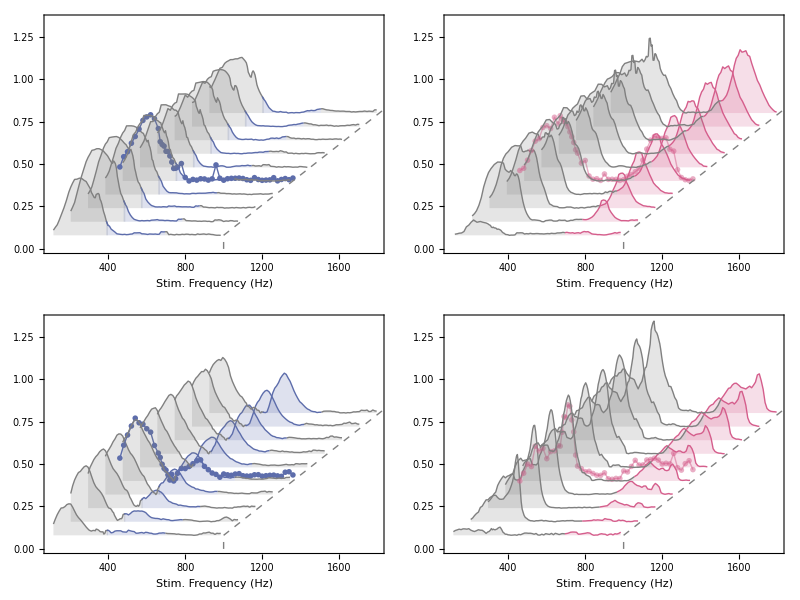

```mathematica
pltRangeRidge=  {{100,1800},{0,1.35}};
pointSizeRidge = 3;
takeEveryXPoints = 2; (*1 for all, 2 for every second...*)

(* 1T SSO nerve *)
testData = MapAt[#*.5Max[ridge1T[[5]][[;;,2]]]&,rescaler[dat["nerve1T","sso"]][[;;,{1,2}]],{All,2}];
testPlot = ListLinePlot[MapAt[#+(5-1) hoffset&,testData+ voffset (5)-Min[testData[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],col1TN}(*,Filling->voffset*5+Min[testData[[;;,2]]]*)];
minFils = Min[#[[;;,2]]]&/@ridge1T;
allplots1TS = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,col1TN,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge1Ta,ridge1Tb,ridge1Tc}ᵀ,minFils}];
allplots1TS[[5]] =Show[Reverse@{allplots1TS[[5]],testPlot}];

(* 2T SSO nerve *)
testData2TS = MapAt[#*.5Max[ridge2TS[[5]][[;;,2]]]&,rescaler[dat["nerve2T","sso"]][[;;,{1,2}]],{All,2}];
testPlot2TS = ListLinePlot[MapAt[#+(5-1) hoffset&,testData2TS+ voffset (5)-Min[testData2TS[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],color2T,Opacity[0.5]}(*,Filling->voffset*5+Min[testData2TS[[;;,2]]]*)];
minFils2T = Min[#[[;;,2]]]&/@ridge2TS;
allplots2TS = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,color2T,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData2T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge2TaS,ridge2TbS}ᵀ,minFils2T}];
allplots2TS[[5]] =Show[Reverse@{allplots2TS[[5]],testPlot2TS}];

(* 1T quiescent nerve *)
testData1TQ = MapAt[#*.5Max[ridge1TQ[[5]][[;;,2]]]&,rescaler[dat["nerve1T","quies"]][[;;,{1,2}]],{All,2}];
testPlot1TQ = ListLinePlot[MapAt[#+(5-1) hoffset&,testData1TQ+ voffset (5)-Min[testData1TQ[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],col1TN}(*,Filling->voffset*5+Min[testData1TQ[[;;,2]]]*)];
minFils = Min[#[[;;,2]]]&/@ridge1TQ;
allplots1TQ = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,col1TN,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData1T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge1TaQ,ridge1TbQ,ridge1TcQ}ᵀ,minFils}];
allplots1TQ[[5]] =Show[Reverse@{allplots1TQ[[5]],testPlot1TQ}];

(* 2T quiescent nerve *)
testData2T = MapAt[#*.5Max[ridge2T[[5]][[;;,2]]]&,rescaler[dat["nerve2T","quies"]][[;;,{1,2}]],{All,2}];
testPlot2T = ListLinePlot[MapAt[#+(5-1) hoffset&,testData2T+ voffset (5)-Min[testData2T[[;;,2]]] ,{All,1}][[;; ;;takeEveryXPoints]],PlotMarkers->fm2["Circle",pointSizeRidge,1],PlotStyle->{AbsoluteThickness[1],color2T,Opacity[0.5]}(*,Filling->voffset*5+Min[testData2T[[;;,2]]]*)];
minFils2T = Min[#[[;;,2]]]&/@ridge2T;
allplots2TQ = MapThread[
ListLinePlot[#1,
PlotStyle->({#,AbsoluteThickness[1]}&/@{Gray,color2T,Gray}),
FrameLabel->{"Stim. Frequency (Hz)",None},
Filling->Table[i->#2,{i,Length@#1}],
PlotRange->pltRangeRidge,
Frame->{True,False,False,False},
FrameStyle->Directive[Black,FontSize->8],
Epilog->{Dashed,Gray, Line[{{1000,voffset},{1000+(Length@rData2T+1.5)*hoffset,1}}],Line[{{1000,0},{1000,voffset}}]}]&,{{ridge2Ta,ridge2Tb}ᵀ,minFils2T}];
allplots2TQ[[5]] =Show[Reverse@{allplots2TQ[[5]],testPlot2T}];

Grid[{{ampScale1TQv2 = Show[allplots1TQ],ampScale2TQv2 = Show[allplots2TQ]},
{ampScale1TSv2 = Show[allplots1TS],ampScale2TSv2 = Show[allplots2TS]}}]
```

### Panel D

```mathematica
Clear[normalising]
normalising[data_]:=(data-Min[data])/(Max[data]-Min[data]);
opts3 = {Frame->True,FrameStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}],LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}]};


Clear[dataExtractor]
dataExtractor[data_,range_,type_:"nerve"]:=Block[{dat,mean,std,median,lowQ,highQ},
dat = Table[Max[Select[data[[j]][type][[i]],Between[#[[1]],range]&][[;;,3]]],{j,Length@data},{i,10}];
dat = (normalising/@dat)ᵀ;

mean = Mean/@dat;
std = StandardDeviation/@dat;
MapThread[Around[#1,#2]&,{mean,std}]

(*median = Median/@dat;
lowQ = Quantile[#,0.16]&/@dat;
highQ = Quantile[#,0.84]&/@dat;
MapThread[Around[#1,{#1-#2,#3-#1}]&,{median,lowQ,highQ}]*)
]

Clear[fitPower,header]

header[data_]:= If[Length[#]<2,Around[#,0.03],#]&/@data;
fitPower[data_,model_:A x^(-1/b)+c] := Block[{dat,vals,weights},
dat = header[data];
vals = dat[[;;,1]];
weights = dat[[;;,2]];
NonlinearModelFit[vals,model,{A,{b,1},c},x,Weights->1/weights]];
```

```mathematica
baseDir = "N:\\Storage Files\\UCL Data\\Anopheles\\";
ssoMoses = {(*4,*)5(*,6*),7,8(*,12*),13,14};
ssoMos = "Mosquito "<>ToString[#]&/@ssoMoses;
quiesMoses = {1,16};
quiesMos = "Mosquito "<>ToString[#]&/@quiesMoses;
{sso1Tdata,sso2Tdata} = (FileNames["*Laser and Nerve*.txt",baseDir<>#<>"\\set_1\\0_overview\\"]&/@ssoMos)ᵀ;
{quies1Tdata,quies2Tdata} = (FileNames["*Laser and Nerve*.txt",baseDir<>#<>"\\set_1\\0_overview\\"]&/@quiesMos)ᵀ;

ssoData1T= Import[#,"RawJSON"]&/@sso1Tdata;
ssoData2T = Import[#,"RawJSON"]&/@sso2Tdata;

quiesData1T = Import[#,"RawJSON"]&/@quies1Tdata;
quiesData2T = Import[#,"RawJSON"]&/@quies2Tdata;

sso1TRange = {400,700};
quies2TRange = {750,1000};
flagellarRange = {330,400};
baseNerveRange = {100,300};
```

```mathematica
q1Tfit200 = fitPower[dataExtractor[quiesData1T,baseNerveRange,"nerve"]];
q1Tfit510 = fitPower[dataExtractor[quiesData1T,sso1TRange,"nerve"],c];

q2Tfit200 = fitPower[dataExtractor[quiesData2T,baseNerveRange,"nerve"]];
q2Tfit810 = fitPower[dataExtractor[quiesData2T,quies2TRange,"nerve"],A x +c];

sso1Tfit200 = fitPower[dataExtractor[ssoData1T,baseNerveRange,"nerve"]];
sso1Tfit510 = fitPower[dataExtractor[ssoData1T,sso1TRange,"nerve"],A x +c];

sso2Tfit200 = fitPower[dataExtractor[ssoData2T,baseNerveRange,"nerve"]];
sso2Tfit810 = fitPower[dataExtractor[ssoData2T,quies2TRange,"nerve"],A x +c];
```

{A→-0.894887,b→0.60769,c→0.89369}

{A→0.,b→0.,c→0.53992}

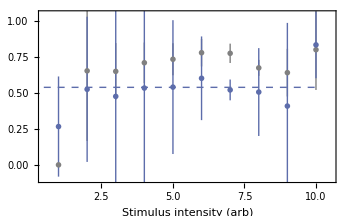
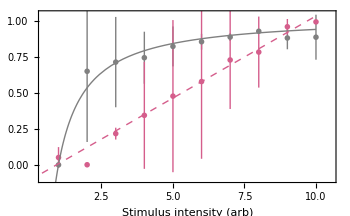
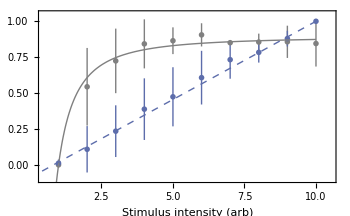
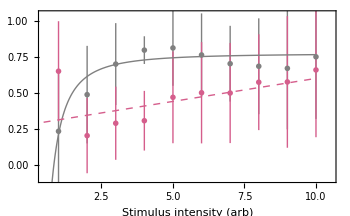

```mathematica
{op11,op22} = {0.5,1};
{c111,c222,c333} = {Gray,blue,Black};
pointSize = 3;

sso1Tfit200["BestFitParameters"]
q1Tfit510["BestFitParameters"]

{{panelD1,panelD2},{panelD3,panelD4}}={{Show[{ListPlot[{dataExtractor[quiesData1T,baseNerveRange,"nerve"],dataExtractor[quiesData1T,sso1TRange,"nerve"]},
PlotStyle->{c111,c222},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{q1Tfit200[x],q1Tfit510[x]},{x,0,10},PlotStyle->{{AbsoluteThickness[1],c111},{Dashed,AbsoluteThickness[1],c222}}]}],

 Show[{ListPlot[{dataExtractor[quiesData2T,baseNerveRange,"nerve"],dataExtractor[quiesData2T,sso1TRange,"nerve"]},
PlotStyle->{c111,color2T},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{q2Tfit200[x],q2Tfit810[x]},{x,0,10},PlotStyle->{{AbsoluteThickness[1],c111},{Dashed,AbsoluteThickness[1],color2T}}]}]},

{Show[{ListPlot[{dataExtractor[ssoData1T,baseNerveRange,"nerve"],dataExtractor[ssoData1T,sso1TRange,"nerve"]},
PlotStyle->{c111,c222},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{sso1Tfit200[x],sso1Tfit510[x]},{x,0,10},PlotStyle->{{AbsoluteThickness[1],c111},{Dashed,AbsoluteThickness[1],c222}}]}],

Show[{ListPlot[{dataExtractor[ssoData2T,baseNerveRange,"nerve"],dataExtractor[ssoData2T,quies2TRange,"nerve"]},
PlotStyle->{c111,color2T},Frame->{True,True,False,False}, opts3,FrameLabel->{"Stimulus intensity (arb)",None},PlotRange->{{0.5,10.5},{-0.1,1.05}},
PlotMarkers->{fm2["Circle",pointSize,op11],fm2["Diamond",pointSize,op22]},IntervalMarkers->{"Bars","Fences"}],
Plot[{sso2Tfit200[x],sso2Tfit810[x]},{x,0,10},PlotStyle->{{AbsoluteThickness[1],c111},{Dashed,AbsoluteThickness[1],color2T}}]}]}}
```

### Final Plot of Fig.1

```mathematica
smallFigSize = 0.6;
rowSize = 1;
plotGrid[{
{aga1T[[1]],aga2T[[1]],nquies1T350Hz,nquies2T350Hz,nquies510,nquies810},
{aga1T[[2]],aga2T[[2]],nwsso3601T,nwsso3602T,nwsso510,nwsso810},
{aga1T[[3]],aga2T[[3]],nsso3551T,nsso3552T,nsso510,nsso810},
{ampScale1TQv2,ampScale2TQv2,panelD1,SpanFromLeft,panelD2,SpanFromLeft},
{ampScale1TSv2,ampScale2TSv2,panelD3,SpanFromLeft,panelD4,SpanFromLeft}},

ImageSize->165*3.78 4.3/5,
ItemSize->{{GoldenRatio 1,GoldenRatio,smallFigSize,smallFigSize,smallFigSize,smallFigSize}(* columns*),{rowSize,rowSize,rowSize,1.5,1.5}(* rows*)},
Spacings->{{0,25,5,15,5}(*columns separation*),{0,0,20,25}(* row separation*)},
Method->{"FixFrameTicks"->False,"AllCustomTicks"->Automatic}]
```

-Graphics-

## Figure 4 - precision vs mechanical state

### Anopheles

```mathematica
data = Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\fig_data_Anopheles.xlsx","XLSX"];
labels = {"plot1_raw","plot1_summary","plot1_ttests","plot2_raw","plot2_summary","plot2_ttests","plot3_raw","plot3_summary"};

(*------------------------------------- OPTIONS ---------------------------------*)
opts = {Frame->True,FrameStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}],LabelStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}]};
(*------------------------------------- OPTIONS ---------------------------------*)
```

#### Fig.4a

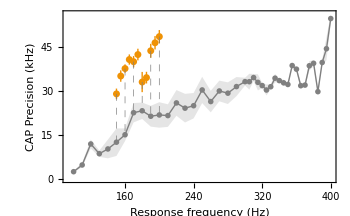

```mathematica
headers=First[data[[2]]];
rows=Rest[data[[2]]];
dt=Dataset[Map[AssociationThread[headers,#]&,rows]];
rescale[data_]:=MapAt[1. 10^-3 #&,data,{All,2}]

dt1 = dt[Select[#"tone_type" =="1T"& ]][All,<|#,"upper_lim"->#"mean_precision"+#"sem_precision","lower_lim"->#"mean_precision"-#"sem_precision"|>&];
dt2 = dt[Select[#"tone_type" =="2T"& ]][All,<|#,"mean_error"->Around[#"mean_precision",#"sem_precision"]|>&];

inter=Interpolation[Normal[rescale@dt1[All,{"Distortion","mean_precision"}][Values]]]; (* interpolation of the 1T curve*)
commonFrequencies = Normal[rescale@dt1[All,{"Distortion","mean_precision"}][Values]][[;;,1]] ∩ Normal[rescale@dt2[All,{"Distortion","mean_precision"}][Values]][[;;,1]];(* which frequencies exist in the 2T dataset *)
pointsOfContact = inter[#]&/@ commonFrequencies;(* where the 2T points intersect the 1T interpolation *)

common1T = Select[Normal[rescale@dt1[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
common2T = Select[Normal[rescale@dt2[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
lines = Line/@({common2T,common1T}ᵀ);


{c1,c2} = {Gray,orange};
fig6a = Show[{
ListLinePlot[{rescale@dt1[All,{"Distortion","upper_lim"}][Values],rescale@dt1[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->Full,
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],lines}],
ListLinePlot[rescale@dt1[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1}],
ListPlot[{rescale@dt1[All,{"Distortion","mean_precision"}][Values],rescale@dt2[All,{"Distortion","mean_error"}][Values]},PlotStyle->{{AbsolutePointSize[4],c1},{AbsolutePointSize[5],c2}}(*,Filling->{2->{1}},FillingStyle->Dashed*)]
}]
```

#### Fig.4b

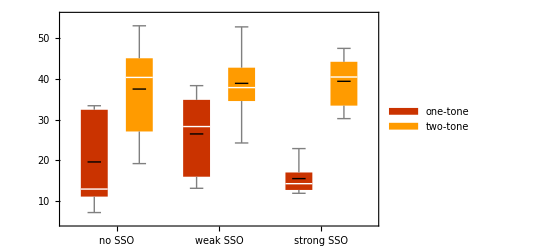

```mathematica
headers=First[data[[4]]];
rows=Rest[data[[4]]];
dplot2 =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)

avgdplot2 = dplot2[GroupBy[{#"sso_state",#"tone_type",#Distortion}&]][All,Mean][All,{"Precision"}]; (* group by state, tone type and then by reponse frequency. Take the average (in case we have repeat measurements)*)
flatAvg=Dataset[KeyValueMap[Append[<|"sso_state"->#[[1]],"tone_type"->#[[2]],"Distortion"->#[[3]]|>,#2]&]@Normal[avgdplot2]]; (* flatten the list back into a normal datast*)
paired = flatAvg[GroupBy[{#"sso_state",#"Distortion"}&]][Select[Length[#]==2&]]; (* regroup by state and response frequency and ensure that there are two elements involes (one at 1T and one at 2T)*)
extracted = Table[SortBy[dat,#[[2]]&],{dat,Values[Values[Normal[paired]]]}]; (*extract the data into a standard list*)
logVals = GatherBy[({#[[1,1]],#[[1,3]],(#[[2,4]]-#[[1,4]])/#[[1,4]]}&/@extracted),#[[1]]&] ;(* extract the metric at hand. Initially it was just Log[p2T/p1T] but in the end went with gain (P2T - P1T)/P1T*)

stateSeperated = GatherBy[Flatten[Normal[flatAvg[GroupBy[{#"sso_state",#"tone_type"}&],All,{"sso_state","tone_type","Precision"}][Values,Values]],1],#[[1]]&];
toneSeparated =Table[ GatherBy[dat,#[[2]]&][[;;,;;,-1]]*10^-3,{dat,stateSeperated}];
fig6b = BoxWhiskerChart[toneSeparated,"Mean",ChartLabels->{{"no SSO","weak SSO","strong SSO"},None},PlotTheme->"Web",ChartLegends->{"one-tone","two-tone"}]
```

#### Fig.4c

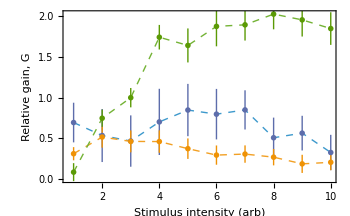

```mathematica
headers=First[data[[-1]]];
rows=Rest[data[[-1]]];
dplot3 =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)

d1 = dplot3[All,<|#,"prec" ->Around[#"mean_precision"*10^-3,#"sem_precision"*10^-3]|>&][All,{"Tone type","SSO state","Amp","prec"}]; (* collapsing mean and error columns into one using Around*)
d2 = d1[GroupBy[{#"SSO state",#"Amp"}&]][Values,Values]//Normal;
d3 =GatherBy[( {#[[1,3]],(#[[2,-1]]-#[[1,-1]])/#[[1,-1]],#[[1,2]]}&/@d2),#[[-1]]&];

lgds = SwatchLegend[ColorData[97,#]&/@{3,2,1},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,6,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6c =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3[[;;,;;,;;2]],
PlotStyle->Directive@{AbsoluteThickness[1],Dashed},
opts,
FrameLabel->{"Stimulus intensity (arb)","Relative gain, G"},
Epilog->Inset[lgds,Scaled[{0.15,0.8}]]],
ListPlot[d3[[;;,;;,;;2]],PlotMarkers->(fm2[#,6,0.5]&/@{"Circle","Square","Diamond"})]}]
```

#### Final Plotting - Anopheles

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Web",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}

```mathematica
{c1,c2} = {Black,Blend[{Lighter@purple,Gray},0.35]};
{op1,op2}= {.8,0.5};
plt6Range = {{94,400},{0,56}};
fig6aMarkerSize =3;
lgds2 = SwatchLegend[{c2,c1},{"𝒻_1 + 1.5 𝒻_1"(*"1T + 1.5×𝒻"*),"𝒻_1"},LegendMarkers->(fm2["Circle",fig6aMarkerSize+1,#]&/@{op2,.5})];

fig6a = Show[{
(*1T upper and lower limits*)
ListLinePlot[{rescale@dt1[All,{"Distortion","upper_lim"}][Values],rescale@dt1[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->{0,58},
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},Frame->{True,True,False,False},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],lines,Inset[lgds2,Scaled[{0.85,0.25}]]}],
(*1T means*)
ListLinePlot[rescale@dt1[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1(*c1*)},PlotMarkers->(fm2["Circle",fig6aMarkerSize,0.5])],
(*2T means*)
ListPlot[{
rescale@dt1[All,{"Distortion","mean_precision"}][Values],
rescale@dt2[All,{"Distortion","mean_error"}][Values],
rescale@dt1[Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_precision"}][Values]
(*rescale@dt1[All,<|#,"mean_err"->Around[#"mean_precision",#"sem_precision"]|>&][Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_err"}][Values]*)},PlotStyle->{{AbsolutePointSize[4],Lighter@c1},{AbsolutePointSize[5],c2},{AbsolutePointSize[4],Darker@c1}}(*,Filling->{2->{1}},FillingStyle->Dashed*),
PlotMarkers->{fm2["Circle",fig6aMarkerSize,op1],fm2["Circle",fig6aMarkerSize,.5],fm2["Circle",1.1fig6aMarkerSize, op2]}]
}(*,Prolog->{EdgeForm[Directive[Gray,Thin,Opacity[0.2]]],Opacity[0.1],Gray,Rectangle[{145,0},{205,45}]}*)];


blendRatio = 0.2;
{c1,c2,c3} =Blend[{#,Gray},blendRatio]&/@{blue,orange,red};
fig6b =BoxWhiskerChart[Flatten[toneSeparated,1],"Mean",ChartLabels->{{"no SSO","weak SSO","SSO"},{"",""}(*{"1T","2T"}*)}
,Frame->{{True,False},{True,False}},FrameLabel->{{None,None},{None,None}},FrameStyle->{{StrokeForm[Opacity[0]],StrokeForm[Opacity[0]]},{Automatic,None}},FrameTicks->Automatic,
(*ChartLegends->{"one-tone","two-tone"},*)
ChartStyle->Directive/@{{Lighter@c1},{c1},{Lighter@c2},{c2},{Lighter@c3},{c3}},
LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}]];

lgds = SwatchLegend[Reverse@{c1,c2,c3},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,fig6aMarkerSize+1,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6c =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3[[;;,;;,;;2]],
PlotStyle->({AbsoluteThickness[1],Dashed,#}&/@{c1,c2,c3}),PlotRange->{{0.5,10.5},{0,2.2}},
opts,
FrameLabel->{"Stimulus intensity (arb)","Relative precision gain, G"}(*,
Epilog->Inset[lgds,Scaled[{0.1,0.75}]]*)],
ListPlot[d3[[;;,;;,;;2]],PlotStyle->{c1,c2,c3},PlotMarkers->(fm2[#,fig6aMarkerSize,.5]&/@{"Circle","Square","Diamond"})]}];
```

```mathematica
plotGrid[{
{fig6a,fig6b,None},
{fig6c,SpanFromLeft,None}},

ImageSize->165*3.78 4.7/5,
ItemSize->{{GoldenRatio,.8,GoldenRatio,1}(* columns*),{.8GoldenRatio,GoldenRatio}(* rows*)},
Spacings->{{30}(*columns separation*),{50}(* row separation*)}]
```

-Graphics-

```mathematica
cols
```

{RGBColor[0.3666665, 0.4254905, 0.6725490000000001],RGBColor[0.937255, 0.572549, 0.0196078],RGBColor[0.356863, 0.603922, 0.0196078],RGBColor[0.733333, 0.14902, 0.345098],RGBColor[0.619608, 0.0705882, 0.854902],RGBColor[0, 0.701961, 1],RGBColor[0.741176, 0.0156863, 0.160784],RGBColor[0.898039, 0.466667, 0.156863],RGBColor[0.513725, 0.713725, 0.152941],RGBColor[0.0392157, 0.219608, 0.286275]}

```mathematica
Export[expDir<>"figure_6_precision_B.pdf",%,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_6_precision_B.pdf

### Aedes

```mathematica
data = Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\fig_data_Aedes.xlsx","XLSX"];
labels = {"plot1_raw","plot1_summary","plot1_ttests","plot2_raw","plot2_summary","plot2_ttests","plot3_raw","plot3_summary"};

(*------------------------------------- OPTIONS ---------------------------------*)
opts = {Frame->True,FrameStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}],LabelStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}]};
(*------------------------------------- OPTIONS ---------------------------------*)
```

#### Fig.4a

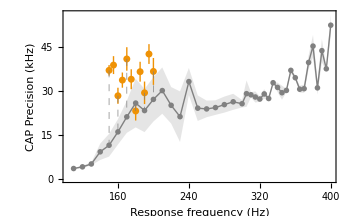

```mathematica
headers=First[data[[2]]];
rows=Rest[data[[2]]];
dt=Dataset[Map[AssociationThread[headers,#]&,rows]];
rescale[data_]:=MapAt[1. 10^-3 #&,data,{All,2}]

dt1AA = dt[Select[#"tone_type" =="1T"& ]][All,<|#,"upper_lim"->#"mean_precision"+#"sem_precision","lower_lim"->#"mean_precision"-#"sem_precision"|>&];
dt2AA = dt[Select[#"tone_type" =="2T"& ]][All,<|#,"mean_error"->Around[#"mean_precision",#"sem_precision"]|>&];

inter=Interpolation[Normal[rescale@dt1AA[All,{"Distortion","mean_precision"}][Values]]]; (* interpolation of the 1T curve*)
commonFrequencies = Normal[rescale@dt1AA[All,{"Distortion","mean_precision"}][Values]][[;;,1]] ∩ Normal[rescale@dt2AA[All,{"Distortion","mean_precision"}][Values]][[;;,1]];(* which frequencies exist in the 2T dataset *)
pointsOfContact = inter[#]&/@ commonFrequencies;(* where the 2T points intersect the 1T interpolation *)

common1TAA = Select[Normal[rescale@dt1AA[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
common2TAA = Select[Normal[rescale@dt2AA[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
linesAA= Line/@({common2TAA,common1TAA}ᵀ);


{c1,c2} = {Gray,orange};
fig6a = Show[{
ListLinePlot[{rescale@dt1AA[All,{"Distortion","upper_lim"}][Values],rescale@dt1AA[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->Full,
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],linesAA}],
ListLinePlot[rescale@dt1AA[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1}],
ListPlot[{rescale@dt1AA[All,{"Distortion","mean_precision"}][Values],rescale@dt2AA[All,{"Distortion","mean_error"}][Values]},PlotStyle->{{AbsolutePointSize[4],c1},{AbsolutePointSize[5],c2}}(*,Filling->{2->{1}},FillingStyle->Dashed*)]
}]
```

#### Fig.4b

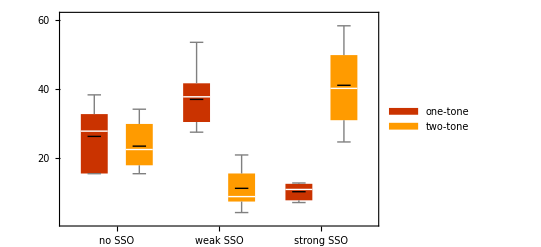

```mathematica
headers=First[data[[4]]];
rows=Rest[data[[4]]];
dplot2 =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)

avgdplot2 = dplot2[GroupBy[{#"sso_state",#"tone_type",#Distortion}&]][All,Mean][All,{"Precision"}]; (* group by state, tone type and then by reponse frequency. Take the average (in case we have repeat measurements)*)
flatAvg=Dataset[KeyValueMap[Append[<|"sso_state"->#[[1]],"tone_type"->#[[2]],"Distortion"->#[[3]]|>,#2]&]@Normal[avgdplot2]]; (* flatten the list back into a normal datast*)
paired = flatAvg[GroupBy[{#"sso_state",#"Distortion"}&]][Select[Length[#]==2&]]; (* regroup by state and response frequency and ensure that there are two elements involes (one at 1T and one at 2T)*)
extracted = Table[SortBy[dat,#[[2]]&],{dat,Values[Values[Normal[paired]]]}]; (*extract the data into a standard list*)
logVals = GatherBy[({#[[1,1]],#[[1,3]],(#[[2,4]]-#[[1,4]])/#[[1,4]]}&/@extracted),#[[1]]&] ;(* extract the metric at hand. Initially it was just Log[p2T/p1T] but in the end went with gain (P2T - P1T)/P1T*)

stateSeperatedAA= GatherBy[Flatten[Normal[flatAvg[GroupBy[{#"sso_state",#"tone_type"}&],All,{"sso_state","tone_type","Precision"}][Values,Values]],1],#[[1]]&];
toneSeparatedAA =Table[ GatherBy[dat,#[[2]]&][[;;,;;,-1]]*10^-3,{dat,stateSeperatedAA}];
fig6b = BoxWhiskerChart[toneSeparatedAA,"Mean",ChartLabels->{{"no SSO","weak SSO","strong SSO"},None},PlotTheme->"Web",ChartLegends->{"one-tone","two-tone"}]
```

#### Fig.4c

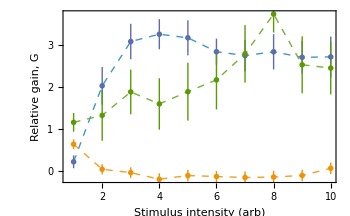

```mathematica
headers=First[data[[-1]]];
rows=Rest[data[[-1]]];
dplot3AA =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)

d1AA = dplot3AA[All,<|#,"prec" ->Around[#"mean_precision"*10^-3,#"sem_precision"*10^-3]|>&][All,{"Tone type","SSO state","Amp","prec"}]; (* collapsing mean and error columns into one using Around*)
d2AA = d1AA[GroupBy[{#"SSO state",#"Amp"}&]][Values,Values]//Normal;
d3AA =GatherBy[( {#[[1,3]],(#[[2,-1]]-#[[1,-1]])/#[[1,-1]],#[[1,2]]}&/@d2AA),#[[-1]]&];

lgds = SwatchLegend[ColorData[97,#]&/@{3,2,1},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,6,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6c =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3AA[[;;,;;,;;2]],
PlotStyle->Directive@{AbsoluteThickness[1],Dashed},
opts,
FrameLabel->{"Stimulus intensity (arb)","Relative gain, G"},
Epilog->Inset[lgds,Scaled[{0.15,0.8}]]],
ListPlot[d3AA[[;;,;;,;;2]],PlotMarkers->(fm2[#,6,0.5]&/@{"Circle","Square","Diamond"})]}]
```

#### Final Plotting - Anopheles

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Web",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}

```mathematica
{c1,c2} = {Black,Blend[{Lighter@purple,Gray},0.35]};
{op1,op2}= {.8,0.5};
plt6Range = {{94,400},{0,56}};
fig6aMarkerSize =3;
lgds2 = SwatchLegend[{c2,c1},{"𝒻_1 + 1.5 𝒻_1"(*"1T + 1.5×𝒻"*),"𝒻_1"},LegendMarkers->(fm2["Circle",fig6aMarkerSize+1,#]&/@{op2,.5})];

fig6aAA = Show[{
(*1T upper and lower limits*)
ListLinePlot[{rescale@dt1AA[All,{"Distortion","upper_lim"}][Values],rescale@dt1AA[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->{0,58},
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},Frame->{True,False,False,False},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],linesAA,Inset[lgds2,Scaled[{0.85,0.25}]]}],
(*1T means*)
ListLinePlot[rescale@dt1AA[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1(*c1*)},PlotMarkers->(fm2["Circle",fig6aMarkerSize,0.5])],
(*2T means*)
ListPlot[{
rescale@dt1AA[All,{"Distortion","mean_precision"}][Values],
rescale@dt2AA[All,{"Distortion","mean_error"}][Values],
rescale@dt1AA[Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_precision"}][Values]
(*rescale@dt1[All,<|#,"mean_err"->Around[#"mean_precision",#"sem_precision"]|>&][Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_err"}][Values]*)},PlotStyle->{{AbsolutePointSize[4],Lighter@c1},{AbsolutePointSize[5],c2},{AbsolutePointSize[4],Darker@c1}}(*,Filling->{2->{1}},FillingStyle->Dashed*),
PlotMarkers->{fm2["Circle",fig6aMarkerSize,op1],fm2["Circle",fig6aMarkerSize,.5],fm2["Circle",1.1fig6aMarkerSize, op2]}]
}(*,Prolog->{EdgeForm[Directive[Gray,Thin,Opacity[0.2]]],Opacity[0.1],Gray,Rectangle[{145,0},{205,45}]}*)];


blendRatio = 0.2;
{c1,c2,c3} =Blend[{#,Gray},blendRatio]&/@{blue,orange,red};

fig6bAA =BoxWhiskerChart[Flatten[toneSeparatedAA,1],"Mean",ChartLabels->{{"no SSO","weak SSO","SSO"},{"",""}(*{"1T","2T"}*)}
,Frame->{{True,False},{True,False}},FrameLabel->{{None,None},{None,None}},FrameStyle->{{StrokeForm[Opacity[0]],StrokeForm[Opacity[0]]},{Automatic,None}},FrameTicks->Automatic,
(*ChartLegends->{"one-tone","two-tone"},*)
ChartStyle->Directive/@{{Lighter@c1},{c1},{Lighter@c2},{c2},{Lighter@c3},{c3}},
LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}]];

lgds = SwatchLegend[Reverse@{c1,c2,c3},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,fig6aMarkerSize+1,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6cAA =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3AA[[;;,;;,;;2]],
PlotStyle->({AbsoluteThickness[1],Dashed,#}&/@{c1,c2,c3}),PlotRange->Full,
opts,
FrameLabel->{"Stimulus intensity (arb)",""}(*,
Epilog->Inset[lgds,Scaled[{0.1,0.75}]]*)],
ListPlot[d3AA[[;;,;;,;;2]],PlotStyle->{c1,c2,c3},PlotMarkers->(fm2[#,fig6aMarkerSize,.5]&/@{"Circle","Square","Diamond"})]}];
```

```mathematica
plotGrid[{
{fig6aAA,fig6bAA,None},
{fig6cAA,SpanFromLeft,None}},

ImageSize->165*3.78 4.7/5,
ItemSize->{{GoldenRatio,.8,GoldenRatio,1}(* columns*),{.8GoldenRatio,GoldenRatio}(* rows*)},
Spacings->{{30}(*columns separation*),{50}(* row separation*)}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_6_precision_B.pdf",%,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_6_precision_B.pdf

### Culex

```mathematica
data = Import["C:\\Users\\hadif\\Proton Drive\\c.a.alampounti\\My files\\Uni\\UCL\\Projects\\02_DP Theory paper\\Marcos and Joerg folder (add what you want here)\\Marcos\\fig_data_Culex.xlsx","XLSX"];
labels = {"plot1_raw","plot1_summary","plot1_ttests","plot2_raw","plot2_summary","plot2_ttests","plot3_raw","plot3_summary"};

(*------------------------------------- OPTIONS ---------------------------------*)
opts = {Frame->True,FrameStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}],LabelStyle->Directive[{Black,FontSize->8,FontFamily->"Helvetica"}]};
(*------------------------------------- OPTIONS ---------------------------------*)
```

#### Fig.4a

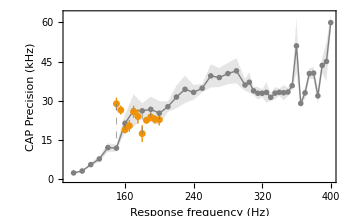

```mathematica
headers=First[data[[2]]];
rows=Rest[data[[2]]];
dt=Dataset[Map[AssociationThread[headers,#]&,rows]];
rescale[data_]:=MapAt[1. 10^-3 #&,data,{All,2}]

dt1CQ = dt[Select[#"tone_type" =="1T"& ]][All,<|#,"upper_lim"->#"mean_precision"+#"sem_precision","lower_lim"->#"mean_precision"-#"sem_precision"|>&];
dt2CQ = dt[Select[#"tone_type" =="2T"& ]][All,<|#,"mean_error"->Around[#"mean_precision",#"sem_precision"]|>&];

inter=Interpolation[Normal[rescale@dt1CQ[All,{"Distortion","mean_precision"}][Values]]]; (* interpolation of the 1T curve*)
commonFrequencies = Normal[rescale@dt1CQ[All,{"Distortion","mean_precision"}][Values]][[;;,1]] ∩ Normal[rescale@dt2CQ[All,{"Distortion","mean_precision"}][Values]][[;;,1]];(* which frequencies exist in the 2T dataset *)
pointsOfContact = inter[#]&/@ commonFrequencies;(* where the 2T points intersect the 1T interpolation *)

common1TCQ = Select[Normal[rescale@dt1CQ[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
common2TCQ = Select[Normal[rescale@dt2CQ[All,{"Distortion","mean_precision"}][Values]],MemberQ[commonFrequencies,#[[1]]]&];
linesCQ= Line/@({common2TCQ,common1TCQ}ᵀ);


{c1,c2} = {Gray,orange};
fig6a = Show[{
ListLinePlot[{rescale@dt1CQ[All,{"Distortion","upper_lim"}][Values],rescale@dt1CQ[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->Full,
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],linesCQ}],
ListLinePlot[rescale@dt1CQ[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1}],
ListPlot[{rescale@dt1CQ[All,{"Distortion","mean_precision"}][Values],rescale@dt2CQ[All,{"Distortion","mean_error"}][Values]},PlotStyle->{{AbsolutePointSize[4],c1},{AbsolutePointSize[5],c2}}(*,Filling->{2->{1}},FillingStyle->Dashed*)]
}]
```

#### Fig.4b

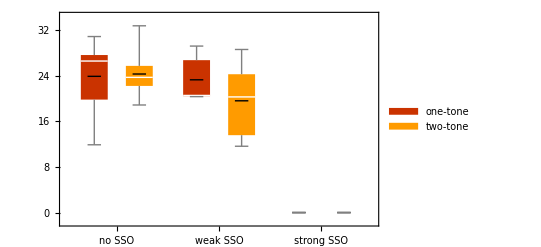

```mathematica
headers=First[data[[4]]];
rows=Rest[data[[4]]];
dplot2 =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)

avgdplot2 = dplot2[GroupBy[{#"sso_state",#"tone_type",#Distortion}&]][All,Mean][All,{"Precision"}]; (* group by state, tone type and then by reponse frequency. Take the average (in case we have repeat measurements)*)
flatAvg=Dataset[KeyValueMap[Append[<|"sso_state"->#[[1]],"tone_type"->#[[2]],"Distortion"->#[[3]]|>,#2]&]@Normal[avgdplot2]]; (* flatten the list back into a normal datast*)
paired = flatAvg[GroupBy[{#"sso_state",#"Distortion"}&]][Select[Length[#]==2&]]; (* regroup by state and response frequency and ensure that there are two elements involes (one at 1T and one at 2T)*)
extracted = Table[SortBy[dat,#[[2]]&],{dat,Values[Values[Normal[paired]]]}]; (*extract the data into a standard list*)
logVals = GatherBy[({#[[1,1]],#[[1,3]],(#[[2,4]]-#[[1,4]])/#[[1,4]]}&/@extracted),#[[1]]&] ;(* extract the metric at hand. Initially it was just Log[p2T/p1T] but in the end went with gain (P2T - P1T)/P1T*)

stateSeperatedCQ= GatherBy[Flatten[Normal[flatAvg[GroupBy[{#"sso_state",#"tone_type"}&],All,{"sso_state","tone_type","Precision"}][Values,Values]],1],#[[1]]&];
stateSeperatedCQ = stateSeperatedCQ[[;;2]];
toneSeparatedCQ =Table[ GatherBy[dat,#[[2]]&][[;;,;;,-1]]*10^-3,{dat,stateSeperatedCQ}];
fig6b = BoxWhiskerChart[toneSeparatedCQ~Join~{{{0},{0}}},"Mean",ChartLabels->{{"no SSO","weak SSO","strong SSO"},None},PlotTheme->"Web",ChartLegends->{"one-tone","two-tone"}]
```

#### Fig.4c

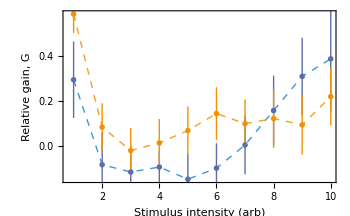

```mathematica
headers=First[data[[-1]]];
rows=Rest[data[[-1]]];
dplot3CQ =Dataset[Map[AssociationThread[headers,#]&,rows]];                   (*import the dataset: 1T runs from 150 - 200 Hz to match the difference tone response frequencies*)

d1CQ = dplot3CQ[All,<|#,"prec" ->Around[#"mean_precision"*10^-3,#"sem_precision"*10^-3]|>&][All,{"Tone type","SSO state","Amp","prec"}]; (* collapsing mean and error columns into one using Around*)
d2CQ = d1CQ[GroupBy[{#"SSO state",#"Amp"}&]][Values,Values]//Normal;
(* CAUTION! THIS IS ONLY FOR CULEX!!!*)
d2CQ = Select[d2CQ,Length@#>1&]; (* exclude the SSO data as we only have 2T versions of them. *)
d3CQ =GatherBy[( {#[[1,3]],(#[[2,-1]]-#[[1,-1]])/#[[1,-1]],#[[1,2]]}&/@d2CQ),#[[-1]]&];

lgds = SwatchLegend[ColorData[97,#]&/@{3,2,1},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,6,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6c =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3CQ[[;;,;;,;;2]],
PlotStyle->Directive@{AbsoluteThickness[1],Dashed},
opts,
FrameLabel->{"Stimulus intensity (arb)","Relative gain, G"},
Epilog->Inset[lgds,Scaled[{0.15,0.8}]]],
ListPlot[d3CQ[[;;,;;,;;2]],PlotMarkers->(fm2[#,6,0.5]&/@{"Circle","Square","Diamond"})]}]
```

#### Final Plotting - Anopheles

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Web",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014]}

```mathematica
{c1,c2} = {Black,Blend[{Lighter@purple,Gray},0.35]};
{op1,op2}= {.8,0.5};
plt6Range = {{94,400},{0,56}};
fig6aMarkerSize =3;
lgds2 = SwatchLegend[{c2,c1},{"𝒻_1 + 1.5 𝒻_1"(*"1T + 1.5×𝒻"*),"𝒻_1"},LegendMarkers->(fm2["Circle",fig6aMarkerSize+1,#]&/@{op2,.5})];

fig6aCQ= Show[{
(*1T upper and lower limits*)
ListLinePlot[{rescale@dt1CQ[All,{"Distortion","upper_lim"}][Values],rescale@dt1CQ[All,{"Distortion","lower_lim"}][Values]},Filling->1->{2},PlotStyle->{Opacity[0]},FillingStyle->Directive[{Opacity[0.2],c1}],PlotRange->{0,58},
FrameLabel->{"Response frequency (Hz)","CAP Precision (kHz)"},Frame->{True,False,False,False},
opts,
Epilog->{Dashed,Gray,AbsoluteThickness[.5],linesCQ,Inset[lgds2,Scaled[{0.85,0.25}]]}],
(*1T means*)
ListLinePlot[rescale@dt1CQ[All,{"Distortion","mean_precision"}][Values],PlotStyle->{AbsoluteThickness[1],c1(*c1*)},PlotMarkers->(fm2["Circle",fig6aMarkerSize,0.5])],
(*2T means*)
ListPlot[{
rescale@dt1CQ[All,{"Distortion","mean_precision"}][Values],
rescale@dt2CQ[All,{"Distortion","mean_error"}][Values],
rescale@dt1CQ[Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_precision"}][Values]
(*rescale@dt1[All,<|#,"mean_err"->Around[#"mean_precision",#"sem_precision"]|>&][Select[Between[#Distortion ,{150,200}]&]][All,{"Distortion","mean_err"}][Values]*)},PlotStyle->{{AbsolutePointSize[4],Lighter@c1},{AbsolutePointSize[5],c2},{AbsolutePointSize[4],Darker@c1}}(*,Filling->{2->{1}},FillingStyle->Dashed*),
PlotMarkers->{fm2["Circle",fig6aMarkerSize,op1],fm2["Circle",fig6aMarkerSize,.5],fm2["Circle",1.1fig6aMarkerSize, op2]}]
}(*,Prolog->{EdgeForm[Directive[Gray,Thin,Opacity[0.2]]],Opacity[0.1],Gray,Rectangle[{145,0},{205,45}]}*)];


blendRatio = 0.2;
{c1,c2,c3} =Blend[{#,Gray},blendRatio]&/@{blue,orange,red};

fig6bCQ =BoxWhiskerChart[Flatten[toneSeparatedCQ~Join~{{{0},{0}}},1],"Mean",ChartLabels->{{"no SSO","weak SSO","SSO"},{"",""}(*{"1T","2T"}*)}
,Frame->{{True,False},{True,False}},FrameLabel->{{None,None},{None,None}},FrameStyle->{{StrokeForm[Opacity[0]],StrokeForm[Opacity[0]]},{Automatic,None}},FrameTicks->Automatic,
(*ChartLegends->{"one-tone","two-tone"},*)
ChartStyle->Directive/@{{Lighter@c1},{c1},{Lighter@c2},{c2},{Lighter@c3},{c3}},
LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}]];

lgds = SwatchLegend[Reverse@{c1,c2,c3},Reverse@{"no SSO","wSSO","SSO"},LegendMarkers->(fm2[#,fig6aMarkerSize+1,0.5]&/@Reverse@{"Circle","Square","Diamond"})];
fig6cCQ =Show[{
ListLinePlot[MapAt[#[[1]]&,#,{All,2}]&/@d3CQ[[;;,;;,;;2]],
PlotStyle->({AbsoluteThickness[1],Dashed,#}&/@{c1,c2,c3}),PlotRange->Full,
opts,
FrameLabel->{"Stimulus intensity (arb)",""},
Epilog->Inset[lgds,Scaled[{0.4,0.75}]]],
ListPlot[d3CQ[[;;,;;,;;2]],PlotStyle->{c1,c2,c3},PlotMarkers->(fm2[#,fig6aMarkerSize,.5]&/@{"Circle","Square","Diamond"})]}];
```

```mathematica
plotGrid[{
{fig6aCQ,fig6bCQ,None},
{fig6cCQ,SpanFromLeft,None}},

ImageSize->165*3.78 4.7/5,
ItemSize->{{GoldenRatio,.8,GoldenRatio,1}(* columns*),{.8GoldenRatio,GoldenRatio}(* rows*)},
Spacings->{{30}(*columns separation*),{50}(* row separation*)}]
```

-Graphics-

```mathematica
Export[expDir<>"figure_6_precision_B.pdf",%,ImageResolution->200]
```

C:\Users\hadif\Proton Drive\c.a.alampounti\My files\Uni\UCL\Projects\02_DP Theory paper\images\article figures\Nature submission 2\raw_svg_figures\figure_6_precision_B.pdf

### All species

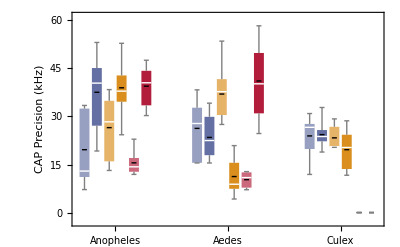

```mathematica
blendRatio = 0.2;
{c1,c2,c3} =Blend[{#,Gray},blendRatio]&/@{blue,orange,red};
fig6bTotal=BoxWhiskerChart[{Flatten[toneSeparated,1],{{},{},{}},Flatten[toneSeparatedAA,1],{{},{},{}},Flatten[toneSeparatedCQ~Join~{{{0},{0}}},1]},"Mean",
ChartLabels->{{"Anopheles","","Aedes","","Culex"},{"",""}(*{"1T","2T"}*)}
,Frame->{{True,False},{True,False}},
FrameLabel->{"",Style["CAP Precision (kHz)",Black]},
ChartLayout->"Grouped",
FrameLabel->{{None,None},{None,None}},
FrameStyle->{{StrokeForm[Opacity[0]],StrokeForm[Opacity[0]]},{Automatic,None}},
FrameTicks->Automatic,FrameTicksStyle->Black,
ChartStyle->Directive/@{{Lighter@c1},{c1},{Lighter@c2},{c2},{Lighter@c3},{c3}},
LabelStyle->Directive[{FontSize->8,FontFamily->"Helvetica"}],opts]
```

```mathematica
(*plotGrid[{
{fig6a,fig6b,fig6aAA,fig6bAA,fig6aCQ,fig6bCQ},
{fig6c,SpanFromLeft,fig6cAA,SpanFromLeft,fig6cCQ,SpanFromLeft}},

ImageSize->165*3.78 5/5,
ItemSize->{{GoldenRatio,.8,GoldenRatio,.8,GoldenRatio,.8}(* columns*),2{.8GoldenRatio,GoldenRatio}(* rows*)},
Spacings->{{30,50,30,50,30}(*columns separation*),{50}(* row separation*)}]*)
```

```mathematica
plotGrid[{
{fig6a,SpanFromLeft,fig6aAA,SpanFromLeft,fig6aCQ,SpanFromLeft},
{fig6bTotal,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft},
{fig6c,SpanFromLeft,fig6cAA,SpanFromLeft,fig6cCQ,SpanFromLeft}},

ImageSize->165*3.78 4.7/5,
ItemSize->{{GoldenRatio,.8,GoldenRatio,.8,GoldenRatio,.8}(* columns*),1.5 {1,.9GoldenRatio,GoldenRatio}(* rows*)},
Spacings->{{30,25,30,25,30}(*columns separation*),{35,30}(* row separation*)}]
```

-Graphics-